```mathematica
Bo= 5*10^(-5); AUcm=1.5*10^13; A=Bo*AUcm*AUcm;Vsw=400*10^5;q=4.8032*10^(-10);mo=1.6726*10^(-24);omega=2*Pi/(27.27*86400);c=3*10^10;
```

```mathematica
GAMMA[r_,th_]:=r*omega*Sin[th]/Vsw
FACTOR1[r_,th_]:=2*p*v*r/(3*q*A*(1+GAMMA[r,th]^2)^2)*(1-2*HeavisideTheta[th-Pi/2])
```

```mathematica
VDr[r_,th_]:=FACTOR1[r,th]*(-GAMMA[r,th]/Tan[th])
```

```mathematica
VDth[r_,th_]:=FACTOR1[r,th]*(2+GAMMA[r,th]^2)*GAMMA[r,th]
```

```mathematica
VDph[r_,th_]:=FACTOR1[r,th]*GAMMA[r,th]^2/Tan[th]
```

```mathematica
r[x_,y_,z_]:=x^2+y^2+z^2
```

```mathematica
th[x_,y_,z_]:=ArcTan[z/Sqrt[x^2+y^2]]
```

```mathematica
ph[x_,y_,z_]:=ArcTan[y/x]
```

```mathematica
Simplify[VDr[r[x,y,z],th[x,y,z]]]
```

(2 omega p v Vsw^3 (x^2+y^2+z^2)^2 (-1+2 HeavisideTheta[-π/2+ArcTan[z/(√(x^2+y^2))]]))/(3 A q √((x^2+y^2+z^2)/(x^2+y^2)) (Vsw^2+omega^2 z^2 (x^2+y^2+z^2))^2)

```mathematica
(*ESTA MATRIZ 'ROTinv' LLEVA DE ESFERICAS A CARTESIANAS......*)
```

```mathematica
r11r[th_,ph_]:=Sin[th]*Cos[ph]
r12r[th_,ph_]:=Sin[th]*Sin[ph]
r13r[th_,ph_]:=Cos[th]
r21r[th_,ph_]:=Cos[th]*Cos[ph]
r22r[th_,ph_]:=Cos[th]*Sin[ph]
r23r[th_,ph_]:=-Sin[th]
r31r[th_,ph_]:=-Sin[ph]
r32r[th_,ph_]:=Cos[ph]
r33r[th_,ph_]:=0
ROT[th_,ph_]:={{r11r[th,ph],r12r[th,ph], r13r[th,ph]},{r21r[th,ph],r22r[th,ph],r23r[th,ph]},{r31r[th,ph],r32r[th,ph],r33r[th,ph]}}
ROTinv[th_,ph_]:=Simplify[Inverse[ROT[th,ph]]]
```

```mathematica
MatrixForm[ROTinv[th,ph]]
```

(Cos[ph] Sin[th] | Cos[ph] Cos[th] | -Sin[ph]
Sin[ph] Sin[th] | Cos[th] Sin[ph] | Cos[ph]
Cos[th] | -Sin[th] | 0)

```mathematica
VDX[x_,y_,z_]:=Simplify[Cos[ph[x,y,z]] *Sin[th[x,y,z]]*VDr[r[x,y,z],th[x,y,z]] + Cos[ph[x,y,z]]*Cos[th[x,y,z]]*VDth[r[x,y,z],th[x,y,z]] - Sin[ph[x,y,z]]*VDph[r[x,y,z],th[x,y,z]]]
```

```mathematica
VDY[x_,y_,z_]:=Simplify[Sin[ph[x,y,z]] *Sin[th[x,y,z]]*VDr[r[x,y,z],th[x,y,z]] + Cos[th[x,y,z]]*Sin[ph[x,y,z]]*VDth[r[x,y,z],th[x,y,z]]  + Cos[ph[x,y,z]]*VDph[r[x,y,z],th[x,y,z]]]
```

```mathematica
VDZ[x_,y_,z_]:=Simplify[Cos[th[x,y,z]]*VDr[r[x,y,z],th[x,y,z]] - Sin[th[x,y,z]]*VDth[r[x,y,z],th[x,y,z]]]
```

```mathematica
v=0.1*c; p=mo*v;
```

```mathematica
VDZ[1,1,0.1]
```

-5.02723×10^-31

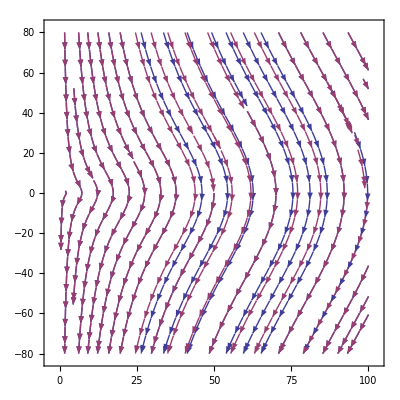

```mathematica
StreamPlot[{{VDX[x,0.001,z],VDZ[x,0.001,z]}, {30.*VDX[x,0.001,z],30.*VDZ[x,0.001,z]}},{x,0.001,100},{z,-80,80}]
```

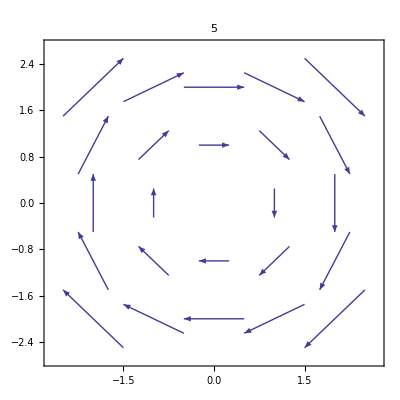
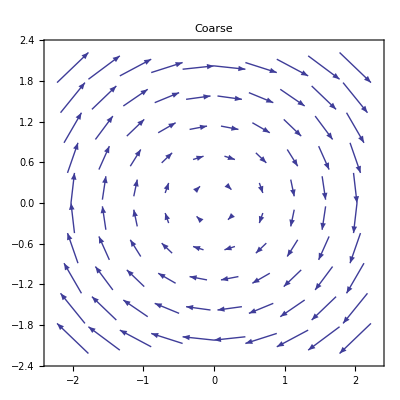
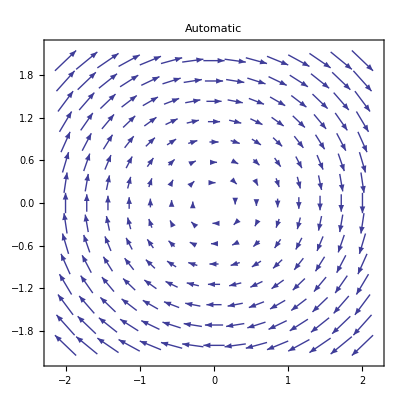

```mathematica
Table[VectorPlot[{y,-x},{x,-2,2},{y,-2,2},PlotLabel->k,VectorPoints->k],{k,{5,Coarse,Automatic}}]
```

```mathematica
Table[VectorPlot[{VDX[x,0.001,z],VDZ[x,0.001,z]},{x,0.001,100},{z,-80,80},PlotLabel->k,VectorPoints->k],{k,{Coarse,Automatic}}]
```

{-Graphics-,-Graphics-}

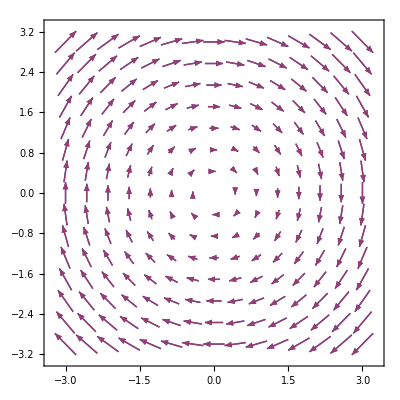

```mathematica
VectorPlot[{{y,-x},{.3*y,-.3*x}},{x,-3,3},{y,-3,3}, VectorPoints->Automatic, VectorScale->Automatic]
```

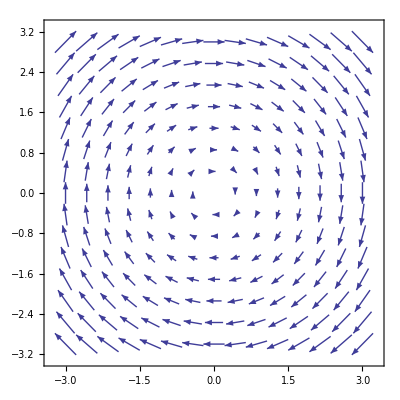

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3}, VectorPoints->Automatic]
```

```mathematica
v=0.9*c
```

2.7×10^10

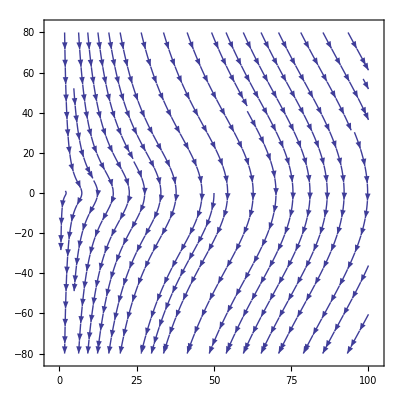

```mathematica
StreamPlot[{VDX[x,0.001,z],VDZ[x,0.001,z]},{x,0.01,100},{z,-80,80}]
```